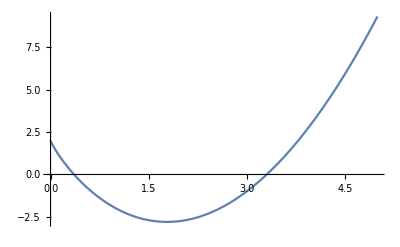

```mathematica
f[x_]:=x Log[3,x]+x^2-5 x+2;
Plot[f[x],{x,0,5}]
```

```mathematica
x0=0.5;
x1=x0-f[x0]/f'[x0];
i = 1;
epsilon=0.001;

While[Abs[x1-x0]>epsilon,
x0=x1;
x1=x0-f[x0]/f'[x0];
i++];
Round[x1, epsilon]
i
```

0.359

3

```mathematica
ClearAll;
x0=0.5;
x1=2;
x2=x1-(f[x1]*(x1-x0))/(f[x1]-f[x0]);
i = 1;
epsilon=0.001;

While[Abs[x1-x0]>epsilon,
x0=x1;
     x1=x2;
     x2=x1-(f[x1]*(x1-x0))/(f[x1]-f[x0]);
i++];
Round[x2, epsilon]
i
```

0.359

7